```mathematica
(*PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]*)
<<Wolfram`QuantumFramework`
```

Paper: https://ieeexplore.ieee.org/document/7515556

```mathematica
RZY[vec_]:=Module[{a,b,ϕ,ψ},
{{a,ϕ},{b,ψ}}=AbsArg[vec];
{{"RZ",ϕ-ψ},{"RY",2 ArcSin[(a-b)/(√(2(a^2+b^2)))]}}]
```

```mathematica
RZYdagger[vec_]:=Module[{a,b,ϕ,ψ},
{{a,ϕ},{b,ψ}}=AbsArg[vec];
{{"RY",-2 ArcSin[(a-b)/(√(2(a^2+b^2)))]},{"RZ",-(ϕ-ψ)}}]
```

```mathematica
multiplexer[qs_,permute_]:=
Module[{vec,qc,qcDagger},
vec=Normal[qs["StateVector"]];
qc=If[MatchQ[permute,{_,0}],
QuantumCircuitOperator[{{"Multiplexer", Sequence@@RZY/@Partition[vec,2]},{"H",qs["Qudits"]}}],
QuantumCircuitOperator[{{"Multiplexer", Sequence@@RZY/@Partition[vec,2]},{"Permutation",Cycles[{permute}]}}]
];
qcDagger=If[MatchQ[permute,{_,0}],
QuantumCircuitOperator[{{"H",qs["Qudits"]},{"Multiplexer", Sequence@@RZYdagger/@Partition[vec,2]}}],
QuantumCircuitOperator[{{"Permutation",Cycles[{permute}]},{"Multiplexer", Sequence@@RZYdagger/@Partition[vec,2]}}]];
Sow[qcDagger];
qc[qs]]
```

```mathematica
stateEvolution[qs_]:=
Module[{n,list},
n=qs["Qudits"];
list=Table[{n,i},{i,n-1,0,-1}];
FoldList[multiplexer,qs,list]]
```

```mathematica
qs=QuantumState[{"RandomPure",5}];
```

```mathematica
stateEvolution[qs]
```

{QuantumState[…],QuantumState[…],QuantumState[…],QuantumState[…],QuantumState[…],QuantumState[…]}

```mathematica
QuantumOperator[{"Multiplexer", Sequence@@RZYdagger/@Partition[qs["StateVector"],2]}->Range[5]]
```

QuantumOperator[…]

```mathematica
QuantumBasis[3,2]
```

QuantumBasis[…]

```mathematica
QuantumOperator[{"Multiplexer", "X","Y","Z"},{1}]
```

QuantumOperator[…]

```mathematica
QuantumOperator[QuantumOperator[{"Multiplexer", "X","Y","Z"},{1}],QuantumBasis[{6}]]
```

QuantumOperator[…]

```mathematica
QuantumCircuitOperator[{QuantumOperator[{"Multiplexer", "X","Y"}]->{1,2}}]["Operators"]
```

{QuantumOperator[…]}

A circuit for generating the state

```mathematica
qc["Flatten"]["Operators"][[;;6]]
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

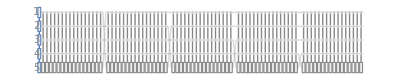

```mathematica
qc=Composition@@Reap[stateEvolution[qs]][[-1,1]];
qc["Flatten"]["Diagram","SubcircuitLevel"->0,"ShowGateLabels"->False]
```

```mathematica
qc[]==qs
```

True

```mathematica
qc
```

QuantumCircuitOperator[<|Elements -> {QuantumOperator[QuantumState[SparseArray[<1024>, {1024}], QuantumBasis[<|Input -> QuditBasis[<|{QuditName[0, Dual -> True], 1} -> SparseArray[<1>, {2}], {QuditName[1, Dual -> True], 1} -> SparseArray[<1>, {2}], {<<2>>} -> <<1>>, <<6>>, {QuditName[1, Dual -> True], 5} -> SparseArray[<1>, {2}]|>], <<4>>|>]], {<<2>>}], <<9>>}, Label -> <<1>>|>]